```mathematica
(* This file compares simulated radial distribution function generated from the crowding.txt Smoldyn file against theoretical results.  It shows essentially perfect agreement. *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sandrews/SSA/software/Smoldyn/trunk/examples/S94_archive/Andrews_2016/excluded volume

```mathematica
maxradius=20
nmolec=6112
volume=1000000
radius=2.5
```

20

6112

1000000

2.5

```mathematica
(* Everything below here should take care of itself *)
```

```mathematica
(* Define functions *)
```

```mathematica
changfunction[h_,x_]:=Module[{Avalue,Bvalue,Cvalue,zd,zs,yplus,yminus,f,a1,a2,a3,b1,b2,b3,b4,b5,b6,c1,c2,c3,c4,c5,c6,c7,c8,c9,H1,H2,H3,g},
Avalue=(-2*h+zd)/(1-h);
Bvalue=(-2h-zd/2)/(1-h);
Cvalue=Sqrt[3]*zs/(2*(1-h));
zd=yplus-yminus;
zs=yplus+yminus;
yplus=(2*h*f)^(1/3)*(Sqrt[2*h^4/f^2+1]+1)^(1/3);
yminus=(2*h*f)^(1/3)*(Sqrt[2*h^4/f^2+1]-1)^(1/3);
f=3+3*h-h^2;
a1=(-2*h*(1-h-3*h^2)+(1-3*h-4*h^2)*zd+(1+h/2)*zd^2)/(3*(2*h^2+zd^2)*(1-h)^2);
a2=(h*(2+4*h-3*h^2)-(1-3*h-4*h^2)*zd+2*(1+h/2)*zd^2)/(3*(2*h^2+zd^2)*(1-h)^2);
a3=((1-3*h-4*h^2)*(4*h^2+zd^2)+h*(2-5*h^2)*zd)/(Sqrt[3]*zs*(2*h^2+zd^2)*(1-h)^2);
b1=-4/3*h*((2*h^2-zd^2)*(1-6*h-3*h^2+20*h^3+15*h^4)+zd*h*(16+24*h-21*h^2-13*h^3+21*h^4))/((2*h^2+zd^2)^3*(1-h)^2);
b2=-b1;
b3=8*Sqrt[3]*h^2*((4*h^2+zd^2)*(2-10*h-24*h^2+30*h^3+79*h^4+21*h^5-17*h^6)+2*zd*h*(16+40*h-h^2-50*h^3+11*h^4+52*h^5+13*h^6))/(zs^3*(2*h^2+zd^2)^3*(1-h)^2);
b4=-2/3*h*(2*h*(10+28*h+21*h^2-13*h^3-19*h^4)+zd*(2-12*h-18*h^2+28*h^3+27*h^4)+zd^2*(4-6*h-18*h^2-7*h^3))/((2*h^2+zd^2)^2*(1-h)^3);
b5=-4/3*h^2*(4*(6-30*h-82*h^2+58*h^3+222*h^4+94*h^5-25*h^6)-zd*(24-10*h-164*h^2-156*h^3+22*h^4+41*h^5)-zd^2*(10+32*h+15*h^2-31*h^3-26*h^4))/(zs^2*(2*h^2+zd^2)^2*(1-h)^3);
b6=4/Sqrt[3]*h^2*(24-10*h-164*h^2-156*h^3+22*h^4+41*h^5-zd*(10+32*h+15*h^2-31*h^3-26*h^4))/(zs*(2*h^2+zd^2)^2*(1-h)^3);
c1=-32*h^3*((2*h^2-zd^2)*(4-56*h-136*h^2+130*h^3+343*h^4-268*h^5-665*h^6-170*h^7+89*h^8)+zd*h*(92+116*h-744*h^2-1468*h^3+332*h^4+1902*h^5+251*h^6-925*h^7-285*h^8))/(zs^2*(2*h^2+zd^2)^5*(1-h)^2);
c2=-c1;
c3=64*Sqrt[3]*h^4*((4*h^2+zd^2)*(24-312*h-1252*h^2-40*h^3+3854*h^4+1658*h^5-6616*h^6-6376*h^7+593*h^8+1799*h^9+107*h^10)+2*zd*h*(276+624*h-1960*h^2-6976*h^3-3208*h^4+8690*h^5+7499*h^6-4996*h^7-6541*h^8-610*h^9+641*h^10))/(zs^5*(2*h^2+zd^2)^5*(1-h)^2);
c4=-8/3*h^2*(2*h*(36-92*h-360*h^2+156*h^3+982*h^4+747*h^5+195*h^6+37*h^7)-3*zd*h*(4+8*h-94*h^2-60*h^3+280*h^4+256*h^5+11*h^6)+zd^2*(4-60*h-84*h^2+190*h^3+150*h^4-258*h^5-185*h^6))/((2*h^2+zd^2)^4*(1-h)^3);
c5=-32*h^4*(96-1248*h-4960*h^2-256*h^3+14976*h^4+7232*h^5-24376*h^6-25632*h^7-724*h^8+5348*h^9+384*h^10-zd*(72-96*h-1152*h^2-932*h^3+3012*h^4+4920*h^5+604*h^6-2286*h^7-708*h^8+211*h^9)+zd^2*(12-24*h-110*h^2+150*h^3+522*h^4-32*h^5-774*h^6-462*h^7-11*h^8))/(zs^4*(2*h^2+zd^2)^4*(1-h)^3);
c6=32*Sqrt[3]*h^4*(72-96*h-1152*h^2-932*h^3+3012*h^4+4920*h^5+604*h^6-2286*h^7-708*h^8+211*h^9+zd*(12-24*h-110*h^2+150*h^3+522*h^4-32*h^5-774*h^6-462*h^7-11*h^8))/(zs^3*(2*h^2+zd^2)^4*(1-h)^3);
c7=2/3*h^2*(4*h*(34+18*h-195*h^2-332*h^3-144*h^4+69*h^5+64*h^6)+2*zd*(2+6*h+30*h^2+176*h^3+174*h^4-66*h^5-79*h^6)+3*zd^2*(4-14*h-32*h^2+32*h^3+68*h^4+23*h^5))/((2*h^2+zd^2)^3*(1-h)^4);
c8=-8/3*h^3*(12+48*h+280*h^2+1224*h^3+1776*h^4-80*h^5-1794*h^6-816*h^7+79*h^8+zd*(36-88*h-420*h^2+72*h^3+1172*h^4+897*h^5-63*h^6-148*h^7)-zd^2*(68+48*h-432*h^2-760*h^3-192*h^4+342*h^5+197*h^6))/(zs^2*(2*h^2+zd^2)^3*(1-h)^4);
c9=8/3*Sqrt[3]*h^3*((4*h^2+zd^2)*(36-88*h-420*h^2+72*h^3+1172*h^4+897*h^5-63*h^6-148*h^7)-zd*(12+48*h+416*h^2+1320*h^3+912*h^4-1600*h^5-2178*h^6-132*h^7+473*h^8))/(zs^3*(2*h^2+zd^2)^3*(1-h)^4);
H1=a1*Exp[Avalue*(x-1)]+a2*Exp[Bvalue*(x-1)]*Cos[Cvalue*(x-1)]+a3*Exp[Bvalue*(x-1)]*Sin[Cvalue*(x-1)];
H2=b1*Exp[Avalue*(x-2)]+
b2*Exp[Bvalue*(x-2)]*Cos[Cvalue*(x-2)]+
b3*Exp[Bvalue*(x-2)]*Sin[Cvalue*(x-2)]+
b4*(x-2)*Exp[Avalue*(x-2)]+
b5*(x-2)*Exp[Bvalue*(x-2)]*Cos[Cvalue*(x-2)]+b6*(x-2)*Exp[Bvalue*(x-2)]*Sin[Cvalue*(x-2)];
H3=c1*Exp[Avalue*(x-3)]+
c2*Exp[Bvalue*(x-3)]*Cos[Cvalue*(x-3)]+
c3*Exp[Bvalue*(x-3)]*Sin[Cvalue*(x-3)]+
c4*(x-3)*Exp[Avalue*(x-3)]+
c5*(x-3)*Exp[Bvalue*(x-3)]*Cos[Cvalue*(x-3)]+
c6*(x-3)*Exp[Bvalue*(x-3)]*Sin[Cvalue*(x-3)]+
c7*(x-3)^2*Exp[Avalue*(x-3)]+
c8*(x-3)^2*Exp[Bvalue*(x-3)]*Cos[Cvalue*(x-3)]+
c9*(x-3)^2*Exp[Bvalue*(x-3)]*Sin[Cvalue*(x-3)];
g=1/x*(HeavisideTheta[x-1]*H1+HeavisideTheta[x-2]*H2+HeavisideTheta[x-3]*H3);
g]
```

```mathematica
(* Load and look at data *)
```

```mathematica
avdensity=N[nmolec/volume]
```

0.006112

```mathematica
simdata=Import["crowdingout.txt","CSV"];
```

```mathematica
simdata
```

{{5.5,0,0,0,0,0,0,0,5.77805×10^-6,0,0,8.85037×10^-6,2.45967×10^-6,0.0000124924,0.0000160666,6.19011×10^-6,0.0000135436,9.56172×10^-6,0.0000138133,0.0000199672,0.000018828,0.0000425908,0.0000950441,0.000232712,0.000801465,0.00279121,0.0179647,0.0166546,0.0141494,0.0117403,0.00984008,0.00839306,0.00745964,0.00662929,0.00600772,0.00547256,0.00507796,0.00485607,0.0046672,0.00451706,0.00450925,0.00456754,0.00461239,0.00489146,0.00505532,0.00531062,0.00567358,0.00600797,0.0063135,0.00665763,0.00695937,0.00716459,0.00726692,0.00722808,0.00708755,0.00678349,0.00663371,0.00637752,0.00624712,0.00606219,0.00585913,0.00581012,0.0056969,0.00567029,0.00567756,0.00566429,0.00570281,0.00579484,0.00589652,0.00596952,0.00605133,0.00618566,0.00626197,0.00633007,0.0063483,0.00636815,0.006415,0.00635345,0.00633372,0.00632936,0.00622871,0.00619819,0.00615933,0.00612766,0.00609269,0.00604293,0.00600454,0.00600137,0.00598364,0.00596488,0.00599787,0.00604462,0.00606115,0.00608822,0.00610129,0.00615042,0.0061876,0.00618918,0.00620912,0.00619282,0.0062012}}

```mathematica
simdata1=Drop[simdata[[1]],1]
```

{0,0,0,0,0,0,0,5.77805×10^-6,0,0,8.85037×10^-6,2.45967×10^-6,0.0000124924,0.0000160666,6.19011×10^-6,0.0000135436,9.56172×10^-6,0.0000138133,0.0000199672,0.000018828,0.0000425908,0.0000950441,0.000232712,0.000801465,0.00279121,0.0179647,0.0166546,0.0141494,0.0117403,0.00984008,0.00839306,0.00745964,0.00662929,0.00600772,0.00547256,0.00507796,0.00485607,0.0046672,0.00451706,0.00450925,0.00456754,0.00461239,0.00489146,0.00505532,0.00531062,0.00567358,0.00600797,0.0063135,0.00665763,0.00695937,0.00716459,0.00726692,0.00722808,0.00708755,0.00678349,0.00663371,0.00637752,0.00624712,0.00606219,0.00585913,0.00581012,0.0056969,0.00567029,0.00567756,0.00566429,0.00570281,0.00579484,0.00589652,0.00596952,0.00605133,0.00618566,0.00626197,0.00633007,0.0063483,0.00636815,0.006415,0.00635345,0.00633372,0.00632936,0.00622871,0.00619819,0.00615933,0.00612766,0.00609269,0.00604293,0.00600454,0.00600137,0.00598364,0.00596488,0.00599787,0.00604462,0.00606115,0.00608822,0.00610129,0.00615042,0.0061876,0.00618918,0.00620912,0.00619282,0.0062012}

```mathematica
nbin=Length[simdata1]
```

100

```mathematica
binwidth=N[maxradius/nbin]
```

0.2

```mathematica
simdata2=simdata1/(nmolec/volume)
```

{0,0,0,0,0,0,0,0.000945362,0,0,0.00144803,0.000402433,0.00204391,0.0026287,0.00101278,0.0022159,0.00156442,0.00226003,0.00326688,0.0030805,0.00696839,0.0155504,0.0380746,0.13113,0.456677,2.93925,2.7249,2.31502,1.92086,1.60996,1.37321,1.22049,1.08464,0.982938,0.89538,0.830818,0.794514,0.763613,0.739048,0.73777,0.747307,0.754645,0.800304,0.827114,0.868884,0.928269,0.982979,1.03297,1.08927,1.13864,1.17222,1.18896,1.1826,1.15961,1.10986,1.08536,1.04344,1.02211,0.99185,0.958627,0.950609,0.932084,0.927731,0.92892,0.926749,0.933051,0.948109,0.964745,0.976688,0.990074,1.01205,1.02454,1.03568,1.03866,1.04191,1.04957,1.0395,1.03628,1.03556,1.0191,1.0141,1.00774,1.00256,0.996841,0.988699,0.982418,0.9819,0.978999,0.975929,0.981327,0.988976,0.99168,0.996109,0.998248,1.00629,1.01237,1.01263,1.01589,1.01322,1.01459}

```mathematica
xvector=Table[i,{i,binwidth/2,maxradius-binwidth/2,binwidth}]
```

{0.1,0.3,0.5,0.7,0.9,1.1,1.3,1.5,1.7,1.9,2.1,2.3,2.5,2.7,2.9,3.1,3.3,3.5,3.7,3.9,4.1,4.3,4.5,4.7,4.9,5.1,5.3,5.5,5.7,5.9,6.1,6.3,6.5,6.7,6.9,7.1,7.3,7.5,7.7,7.9,8.1,8.3,8.5,8.7,8.9,9.1,9.3,9.5,9.7,9.9,10.1,10.3,10.5,10.7,10.9,11.1,11.3,11.5,11.7,11.9,12.1,12.3,12.5,12.7,12.9,13.1,13.3,13.5,13.7,13.9,14.1,14.3,14.5,14.7,14.9,15.1,15.3,15.5,15.7,15.9,16.1,16.3,16.5,16.7,16.9,17.1,17.3,17.5,17.7,17.9,18.1,18.3,18.5,18.7,18.9,19.1,19.3,19.5,19.7,19.9}

```mathematica
Length[xvector]
```

100

```mathematica
simdata2xy=Transpose[{xvector,simdata2}];
```

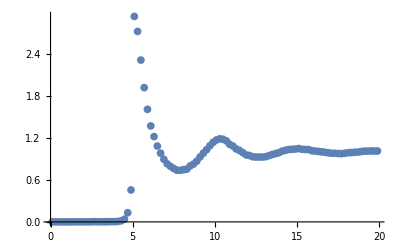

```mathematica
ListPlot[simdata2xy,PlotRange->All]
```

```mathematica
h=Pi*avdensity*(2*radius)^3/6
```

0.400029

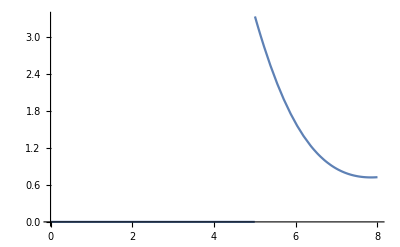

```mathematica
Plot[changfunction[h,x/(2*radius)],{x,0,8}]
```

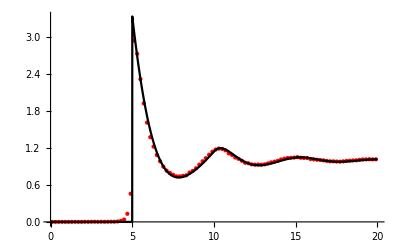

```mathematica
Show[{ListPlot[simdata2xy,PlotStyle->Directive[Red,PointSize[Medium]]],Plot[changfunction[h,x/(2*radius)],{x,0,4*(2*radius)},PlotStyle->Black,Exclusions->None]},PlotRange->All,AxesStyle->Directive[Bold,12]]
```

```mathematica
(* Numbers for hemoglobin *)
```

```mathematica
hgmw=64500
```

64500

```mathematica
hgrad=0.0655*hgmw^(1/3)
```

2.62681

```mathematica
hgdiam=2*hgrad
```

5.25361

```mathematica
hgdiff=N[0.8*3270/hgmw^(1/3)]
```

65.2306

```mathematica
hgsrad=2.5
```

2.5

```mathematica
hgsdiam=2*hgsrad
```

5.

```mathematica
hgsdiff=65
```

65

```mathematica
hgsvol=N[4/3*Pi*hgsrad^3]
```

65.4498

```mathematica
totvol=100^3
```

1000000

```mathematica
hgsnum=0.4*totvol/hgsvol
```

6111.55

```mathematica
hgsdt=(0.1*hgsrad)^2/(2*hgsdiff)
```

0.000480769

```mathematica
(* msd result *)
```

```mathematica
hgsmsd=1495.37
```

1495.37

```mathematica
hgsdiffmsd=hgsmsd/(6*5)
```

49.8457

```mathematica
hgsreldif=hgsdiffmsd/65
```

0.766856

```mathematica
(* diffusion coefficient from Erpenbeck_Wood_1991 *)
```

```mathematica
dspeedy=(3*sigma/(8*nhat*Sqrt[Pi*mass*beta]))*(1-nhat/1.09)*(1+nhat^2*(0.4-0.83*nhat^2))
```

(3 (1-0.917431 nhat) (1+nhat^2 (0.4-0.83 nhat^2)) sigma)/(8 √(beta mass) nhat √π)

```mathematica
nhat=n*sigma^3
```

n sigma^3

```mathematica
dspeedy
```

(3 (1-0.917431 n sigma^3) (1+n^2 sigma^6 (0.4-0.83 n^2 sigma^6)))/(8 √(beta mass) n √π sigma^2)

```mathematica
dspeedy/.{n->6112/1000000,sigma->5}
```

0.393701/(√(beta mass))